```mathematica
<<xlr8r.m
```

reference:
 Chickarmane V, Peterson C (2008) A Computational Model for Understanding Stem Cell, Trophectoderm and Endoderm Lineage Determination. PLoS ONE 3(10): e3478. doi:10.1371/journal.pone.0003478
 
 direct link: http://www.plosone.org/article/info%3Adoi%2F10.1371%2Fjournal.pone.0003478

The figures at the end of the notebook match figure 4 of the cited paper.

```mathematica
net={

{
{{A, 𝒪*𝒮, 𝒪*𝒮*𝒩}, {A, 𝒪, 𝒪*𝒮, 𝒪*𝒮*𝒩, 𝒞*𝒪, 𝒢𝒞}}⟹𝒪, rational[{a0,a1,a2,a3},{1,b0, b1, b2,b3,b4,b5}]
},
{𝒪->∅, γ1},

{
{{𝒪*𝒮,𝒪*𝒮*𝒩},{𝒪,𝒪*𝒮,𝒪*𝒮*𝒩}}⟹𝒮,
rational[{c0,c1,c2}, {1,d0,d1,d2}]
},
{𝒮-> ∅, γ2},

{{{𝒪*𝒮,𝒪*𝒮*𝒩}, {𝒪,𝒪*𝒮,𝒪*𝒮*𝒩, 𝒪*𝒢}}⟹𝒩,
rational[{e0, e1,e2}, {1, f0, f1, f2, f3}]
},
{𝒩-> ∅, γ3},

{{{𝒞},{𝒞,𝒞*𝒪}}⟹𝒞,
rational[{g0,g1},{1,h0,h1}]
}, 
{𝒞->∅, γ4},

{{{𝒞,𝒢},{𝒞,𝒢}}⟹𝒢𝒞,
rational[{i0,i1,i2},{1,j0,j1}]
},
{𝒢𝒞-> ∅, γ5},

{{{𝒪,𝒢},{𝒪,𝒢,𝒩}}⟹𝒢,
rational[{p0,p1,p2},{1,q0,q1,q2}]
},
{𝒢-> ∅, γg},

{A-> A, 1}

};
```

```mathematica
ODE[net]//TableForm
```

A'[t]==0
𝒞'[t]==-γ4 𝒞[t]+(g0+g1 𝒞[t])/(1+h0 𝒞[t]+h1 𝒞[t] 𝒪[t])
𝒢'[t]==-γg 𝒢[t]+(p0+p2 𝒢[t]+p1 𝒪[t])/(1+q1 𝒢[t]+q2 𝒩[t]+q0 𝒪[t])
𝒢𝒞'[t]==(i0+i1 𝒞[t]+i2 𝒢[t])/(1+j0 𝒞[t]+j1 𝒢[t])-γ5 𝒢𝒞[t]
𝒩'[t]==-γ3 𝒩[t]+(e0+e1 𝒪[t] 𝒮[t]+e2 𝒩[t] 𝒪[t] 𝒮[t])/(1+f0 𝒪[t]+f3 𝒢[t] 𝒪[t]+f1 𝒪[t] 𝒮[t]+f2 𝒩[t] 𝒪[t] 𝒮[t])
𝒪'[t]==-γ1 𝒪[t]+(a0+a1 A[t]+a2 𝒪[t] 𝒮[t]+a3 𝒩[t] 𝒪[t] 𝒮[t])/(1+b0 A[t]+b5 𝒢𝒞[t]+b1 𝒪[t]+b4 𝒞[t] 𝒪[t]+b2 𝒪[t] 𝒮[t]+b3 𝒩[t] 𝒪[t] 𝒮[t])
𝒮'[t]==-γ2 𝒮[t]+(c0+c1 𝒪[t] 𝒮[t]+c2 𝒩[t] 𝒪[t] 𝒮[t])/(1+d0 𝒪[t]+d1 𝒪[t] 𝒮[t]+d2 𝒩[t] 𝒪[t] 𝒮[t])

```mathematica
table2={a0-> .001, a1-> 1, a2-> 0.005, a3-> 0.025, 
b0-> 1, b1-> 0.001, b2-> 0.005, b3-> 0.025, b4->  10, b5->  10, γ1->  0.1, c0->  0.001,c1-> 0.005,c2->  0.025, d0->  0.001, d1->  0.005, d2->  0.025, γ2->  0.1, e0->  0.001, e1->  0.1, e2->  0.1, f0->  0.001, f1->  0.1, f2->  0.1,f3-> 10,γ3->  0.1,g0->  0.001, g1->   2, h0->   2, h1->  5, γ4->  0.1, i0->  0.001, i1->  0.1, i2->  0.1, j0->  0.1, j1->  0.1, γs-> 0.1,  p0-> 0.1, p1->  1.0, p2->  2.5 10^-4, q0->  1.0, q1->  2.5 10^-4, q2->  15, γg->  0.1};
```

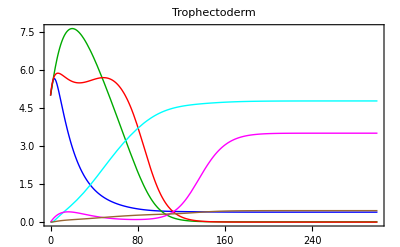

```mathematica
ic={𝒪-> 5,𝒩-> 5,𝒮-> 5,𝒢-> 0,𝒢𝒞->0,𝒞-> 0, A-> 1};
n=run[net, initialConditions-> ic, rates-> table2, timeSpan-> 300];
oplot=runPlot[n,𝒪, PlotStyle-> {Blue,Thick}, holdLegend-> True];
splot=runPlot[n,𝒮,PlotStyle-> {Darker[Green], Thick}, holdLegend-> True];
nplot=runPlot[n,𝒩, PlotStyle-> {Red, Thick}, holdLegend-> True];
cplot=runPlot[n,𝒞, PlotStyle-> {Cyan, Thick}, holdLegend-> True];
gplot=runPlot[n,𝒢, PlotStyle-> {Magenta, Thick}, holdLegend-> True];
gcplot=runPlot[n,𝒢𝒞, PlotStyle-> {Brown, Thick}, holdLegend-> True];
trplot=Show[oplot,splot,nplot,cplot,gplot,gcplot, Frame-> True, PlotLabel-> "Trophectoderm"]
```

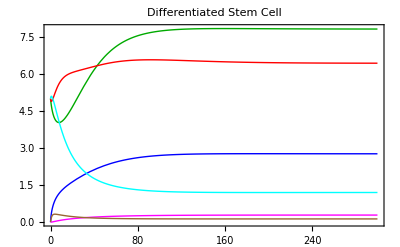

```mathematica
ic={𝒪-> 0,𝒩-> 5,𝒮-> 5,𝒢-> 0,𝒢𝒞->0,𝒞-> 5, A-> 10};
n=run[net, initialConditions-> ic, rates-> table2, timeSpan-> 300];
oplot=runPlot[n,𝒪, PlotStyle-> {Blue,Thick}, holdLegend-> True];
splot=runPlot[n,𝒮,PlotStyle-> {Darker[Green], Thick}, holdLegend-> True];
nplot=runPlot[n,𝒩, PlotStyle-> {Red, Thick}, holdLegend-> True];
cplot=runPlot[n,𝒞, PlotStyle-> {Cyan, Thick}, holdLegend-> True];
gplot=runPlot[n,𝒢, PlotStyle-> {Magenta, Thick}, holdLegend-> True];
gcplot=runPlot[n,𝒢𝒞, PlotStyle-> {Brown, Thick}, holdLegend-> True];
dsplot=Show[oplot,splot,nplot,cplot,gplot,gcplot, Frame-> True, PlotLabel-> "Differentiated Stem Cell"]
```

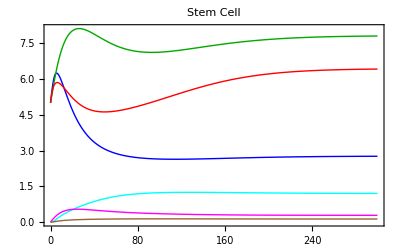

```mathematica
ic={𝒪-> 5,𝒩-> 5,𝒮-> 5,𝒢-> 0,𝒢𝒞->0,𝒞-> 0, A-> 10};
n=run[net, initialConditions-> ic, rates-> table2, timeSpan-> 300];
oplot=runPlot[n,𝒪, PlotStyle-> {Blue,Thick}, holdLegend-> True];
splot=runPlot[n,𝒮,PlotStyle-> {Darker[Green], Thick}, holdLegend-> True];
nplot=runPlot[n,𝒩, PlotStyle-> {Red, Thick}, holdLegend-> True];
cplot=runPlot[n,𝒞, PlotStyle-> {Cyan, Thick}, holdLegend-> True];
gplot=runPlot[n,𝒢, PlotStyle-> {Magenta, Thick}, holdLegend-> True];
gcplot=runPlot[n,𝒢𝒞, PlotStyle-> {Brown, Thick}, holdLegend-> True];
stemplot=Show[oplot,splot,nplot,cplot,gplot,gcplot, Frame-> True, PlotLabel-> "Stem Cell"]
```

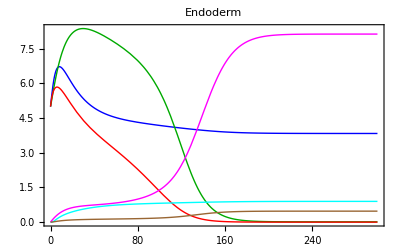

```mathematica
ic={𝒪-> 5,𝒩-> 5,𝒮-> 5,𝒢-> 0,𝒢𝒞->0,𝒞-> 0, A-> 25};
n=run[net, initialConditions-> ic, rates-> table2, timeSpan-> 300];
oplot=runPlot[n,𝒪, PlotStyle-> {Blue,Thick}, holdLegend-> True];
splot=runPlot[n,𝒮,PlotStyle-> {Darker[Green], Thick}, holdLegend-> True];
nplot=runPlot[n,𝒩, PlotStyle-> {Red, Thick}, holdLegend-> True];
cplot=runPlot[n,𝒞, PlotStyle-> {Cyan, Thick}, holdLegend-> True];
gplot=runPlot[n,𝒢, PlotStyle-> {Magenta, Thick}, holdLegend-> True];
gcplot=runPlot[n,𝒢𝒞, PlotStyle-> {Brown, Thick}, holdLegend-> True];
endplot=Show[oplot,splot,nplot,cplot,gplot,gcplot, Frame-> True, PlotLabel-> "Endoderm"]
```